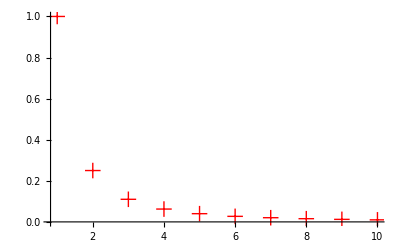
-Graphics-Intensidad [dB]Distancia [m]

```mathematica
ejex ={1, 2, 3, 4, 5, 6, 7, 8, 9, 10};
ejey = {1, 0.25, 0.11, 0.0625, 0.04, 0.027,0.02040, 0.0156, 0.01234,0.01};
Labeled[ListPlot[Transpose[{ejex,ejey}],PlotStyle-> Red, PlotMarkers->{"+", 16}, PlotRange->All], {"Intensidad [dB]", "Distancia [m]"}, {Left, Bottom},RotateLabel->True]
```

```mathematica
linea = Fit[Transpose[{ejex,ejey}],{1, x}, x]
```

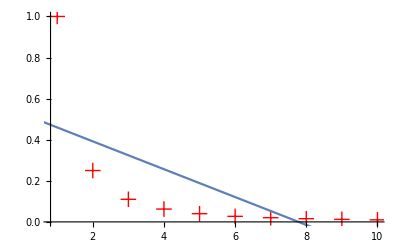
-Graphics-Intensidad [dB]Distancia [m]

```mathematica
Labeled[Show[ListPlot[Transpose[{ejex,ejey}],PlotStyle-> Red, PlotMarkers->{"+", 16}, PlotRange->All],  Plot[linea, {x, 0, 10}]], {"Intensidad [dB]", "Distancia [m]"}, {Left, Bottom},RotateLabel->True]
```

-0.000698099+1.00067/x^2+0.0000730709 x

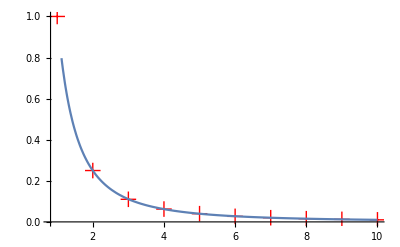
-Graphics-Intensidad [dB]Distancia [m]

```mathematica
parabola=Fit[Transpose[{ejex,ejey}],{1, x, x^-2}, x]
Labeled[Show[ListPlot[Transpose[{ejex,ejey}],PlotStyle-> Red, PlotMarkers->{"+", 16}, PlotRange->All],  Plot[parabola, {x, 0, 10}]], {"Intensidad [dB]", "Distancia [m]"}, {Left, Bottom},RotateLabel->True]
```

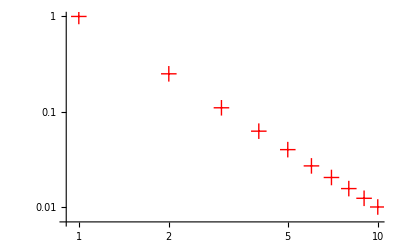
-Graphics-log Intensidad [dB]log Distancia [m]

```mathematica
Labeled[ListLogLogPlot[Transpose[{ejex,ejey}],PlotStyle-> Red, PlotMarkers->{"+", 16}, PlotRange->All],  {"log Intensidad [dB]", "log Distancia [m]"}, {Left, Bottom},RotateLabel->True]
```